## Phase 1 - Simplest Model (HZR)

Humans
In the simplest model, there is a zombie conversion rate Δ - this variable contributes to the reduction in the number of humans. 

Zombies
At the early stage of the apocalypse, we assume that Zombies are still in their rudimentary phase of evolution, they die from running over one another, or from interaction with the world (e.g. crashing into their environment). Their death rate is represented by α. Hence, their population grows with respect to Δ, and decreases with respect to α. 

Graveyard
There is currently no cure found, hence the current conversion process is Humans -> Zombies -> Graveyard. This is the “graveyard”, represented by gDot.

```mathematica
Manipulate[
 solution = NDSolve[
   {
    h'[t] == (-Δ * h[t] * z[t]),
    z'[t] == (-α * z[t]) + (Δ * h[t] * z[t]),
    g'[t] == (α * z[t]),  
    
    (* Initial Conditions *)
    h[0] == 1.0,
    z[0] == 0.01,
    g[0] == 0      
   },
   {h, z, g},      (* Solve for h, z, r *)
   {t, 0, 20}
 ];

 (* 3. Plot *)
 Plot[
  Evaluate[{h[t], z[t], g[t]} /. solution],
  {t, 0, 20},
  
  PlotStyle -> {
    {Blue, Thickness[0.007]},
    {Red, Thickness[0.007]},
    {Purple, Thickness[0.007]}
  },
  PlotLegends -> {"Humans (h)", "Zombies (z)", "Graveyard (g)"},
  AxesLabel -> {"Time (t)", "Population Fractions"},
  PlotRange -> {0, 1.2}, (* Fixed range prevents jumping *)
  PlotLabel -> "Time Evolution of the Apocalypse"
 ],

 (* 4. Sliders *)
 {{Δ, 2, "Attack Rate (Δ)"}, 0.1, 5, 0.01},
 {{α, 1, "Zombie Death Rate (α)"}, 0.1, 2, 0.01}
]
```

#### Phase Space

```mathematica
Manipulate[
 Module[{hCritical},
  
  (* 1. Calculate the critical human population (The Vertical Line) *)
  hCritical = α / Δ;

  (* 2. Combine the Plot and the Line *)
  Show[
   StreamPlot[
    {
     -Δ * h * z,                      (* h' *)
     (-α * z) + (Δ * h * z)           (* z' *)
    },
    {h, 0, 1}, {z, 0, 1}, 
    StreamColorFunction -> "Rainbow",
    FrameLabel -> {"Humans (h)", "Zombies (z)"},
    Frame -> True,
    LabelStyle -> {Bold, 14}
   ],
   
   (* The Critical Threshold Line *)
   Graphics[{
     {Red, Dashed, Thickness[0.007], InfiniteLine[{{hCritical, 0}, {hCritical, 1}}]},
     {Text[Style["Critical Threshold\n(Zombies Die Below This)", Red, 12, Background -> White], {hCritical, 0.8}, {-1.2, 0}]}
    }],
    
   PlotLabel -> Style["Phase Space: Patient Zero", 16, Bold]
  ]
 ],
 
 (* 3. The Sliders *)
 {{Δ, 2, "Attack Rate (Δ)"}, 0.1, 10, 0.01},
 {{α, 1, "Zombie Death Rate (α)"}, 0.1, 5, 0.01}
]
```

### Static Plotting for Report - Phase 1

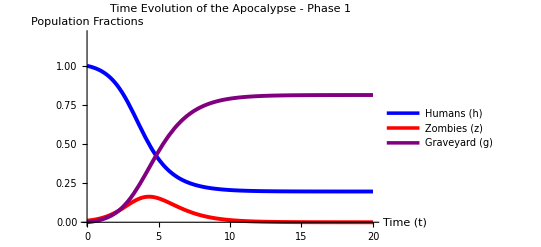

```mathematica
(* 1. Clear and Define Parameters with Default Values *)
Clear[α, Δ, h, z, g, t, solution];
Δ = 2;        (* Attack Rate *)
α = 1;        (* Zombie Death Rate *)

(* 2. Solve the System (NDSolve) *)
solution = NDSolve[
   {
    h'[t] == -Δ * h[t] * z[t],
    z'[t] == -α * z[t] + Δ * h[t] * z[t],
    g'[t] == α * z[t], 
    
    (* Initial Conditions *)
    h[0] == 1.0,
    z[0] == 0.01,
    g[0] == 0
   },
   {h, z, g},      (* Solve for h, z, g *)
   {t, 0, 20}      (* Time 0 to 20 *)
];

(* 3. Plot the Result *)
Plot[
 Evaluate[{h[t], z[t], g[t]} /. solution],
 {t, 0, 20},
 
 (* Styling *)
 PlotStyle -> {
   {Blue, Thickness[0.007]},
   {Red, Thickness[0.007]},
   {Purple, Thickness[0.007]}
 },
 PlotLegends -> {"Humans (h)", "Zombies (z)", "Graveyard (g)"},
 AxesLabel -> {"Time (t)", "Population Fractions"},
 PlotRange -> {0, 1.2}, 
 PlotLabel -> "Time Evolution of the Apocalypse - Phase 1"
]
```

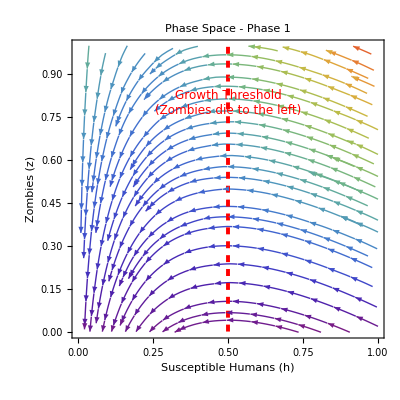

```mathematica
(* 1. Clear and Define Parameters *)
Clear[α, Δ, h, z];
Δ = 2; (* Attack Rate *)
α = 1;        (* Zombie Death Rate *)

(* 2. Calculate the Critical Threshold *)
(* This is the vertical line where zombies start dying *)
hCritical = α / Δ;

(* 3. Generate the Static Plot *)
Show[
 (* A. The Stream Plot (Vector Field) *)
 StreamPlot[
  {
   -Δ * h * z,                  (* h' *)
   -α * z + Δ * h * z    (* z' *)
  },
  {h, 0, 1}, {z, 0, 1},
  StreamColorFunction -> "Rainbow",
  FrameLabel -> {"Susceptible Humans (h)", "Zombies (z)"},
  Frame -> True,
  LabelStyle -> {Black, 14},
  PlotLabel -> Style["Phase Space - Phase 1", 16, Bold]
 ],
 
 (* B. The Critical Threshold Line *)
 Graphics[{
   {Red, Dashed, Thickness[0.007], InfiniteLine[{{hCritical, 0}, {hCritical, 1}}]},
   
   (* Label the line *)
   Text[
    Style["Growth Threshold\n(Zombies die to the left)", Red, 12, Background -> White], 
    {hCritical, 0.8}, {-1.2, 0}
   ],
   
  }],
  
 PlotRange -> {{0, 1}, {0, 1}}
]
```

### Fixed Points Analysis

The fixed points of the system are found by equating the equations to 0.

#### Trace Determinant Diagram

```mathematica
(* 1. Define the Background Map (The "Regions" of Stability) *)
TraceDeterminantBackground[] := Module[{t, d},
  Show[
   (* Draw the Parabola T^2 - 4D = 0 *)
   Plot[t^2/4, {t, -5, 5}, PlotStyle -> {Black, Thickness[0.005]}],
   (* Draw Axes *)
   Graphics[{InfiniteLine[{{0, 0}, {0, 1}}], InfiniteLine[{{0, 0}, {1, 0}}]}],
   Frame -> True, FrameLabel -> {"Trace (T)", "Determinant (D)"},
   PlotLabel -> "Trace-Determinant Diagram"
  ]
 ];

(* 2. Interactive Plot *)
Manipulate[
 Module[{T, D},
  
  (* trace: Using your formula: h - z - alpha *)
  T = (Δ*h) - (Δ*z) - α;
  
  (* determinant: alpha * Delta * z *)
  D = α * Δ * z;
  
  Show[
  TraceDeterminantBackground[],
   Graphics[{
     PointSize[0.04], Blue,
     Point[{T, D}], 
     Text[Style["Your System", Blue, 13, Background -> White], {T, D} + {0, 0.4}]
   }],
   PlotLabel -> Row[{"Trace = ", NumberForm[T, 2], " | Det = ", NumberForm[D, 2]}]
  ]
 ],
 
 {{α, 1, "Zombie Death Rate (α)"}, 0.1, 2},
 {{Δ, 1, "Attack Rate (Δ)"}, 0.1, 2},
 Delimiter,
 {{h, 1, "Current Humans (h)"}, 0, 2},
 {{z, 0, "Current Zombies (z)"}, 0, 2}
]
```

### Stability Analysis

#### Eigen-analysis

When differentiating, 
h’[t] == -Δ * z[t]
z’[t] == -Δh
g’[t] == 0

```mathematica
(* 1. Clear everything to prevent conflicts *)
Clear[h, z, α, Δ];

(* 2. Define the Equations (Right-hand side only) *)
(* We only need h and z for stability analysis *)
equations = {
   -Δ*h*z,                (* h' *)
   -α*z + Δ*h*z    (* z' *)
  };

variables = {h, z};

(* 3. Calculate Jacobian AUTOMATICALLY *)
(* Grad computes the matrix of partial derivatives for you *)
jacobianMatrix = Grad[equations, variables];

(* 4. Define Parameters and Fixed Points *)
parameters = {α -> 1, Δ -> 2};

(* Fixed Point 1: The "Disease Free" State *)
(* h=1 (everyone healthy), z=0 (no zombies) *)
fixedPoint1 = {h -> 1, z -> 0};

(* Fixed Point 2: The "Total Extinction" State *)
(* h=0 (no humans), z=0 (no zombies) *)
fixedPoint2 = {h -> 0, z -> 0};

(* 5. Calculate Eigenvalues *)
(* We replace (.) the variables and parameters into the matrix *)

Print["--- Jacobian at Disease Free State (h=1, z=0) ---"];
matrixP1 = jacobianMatrix /. fixedPoint1 /. parameters;
Print[matrixP1];
Print["Eigenvalues: ", Eigenvalues[matrixP1]];

Print["\n--- Jacobian at Extinction State (h=0, z=0) ---"];
matrixP2 = jacobianMatrix /. fixedPoint2 /. parameters;
Print[matrixP2];
Print["Eigenvalues: ", Eigenvalues[matrixP2]];
```

--- Jacobian at Disease Free State (h=1, z=0) ---

{{0,-2},{0,1}}

Eigenvalues: {1,0}

--- Jacobian at Extinction State (h=0, z=0) ---

{{0,0},{0,-1}}

Eigenvalues: {-1,0}

#### Trace Determinant Diagram - Gemini Generated, need to edit Jacobian

```mathematica
(* 1. Define the Background "Map" Function *)
TraceDeterminantBackground[] := Module[{t, d},
   Show[
    (* Regions *)
    RegionPlot[
     {
      (* Stable Sink (Node) *)
      d > 0 && t < 0 && t^2 - 4 d > 0,
      (* Stable Spiral *)
      d > 0 && t < 0 && t^2 - 4 d < 0,
      (* Unstable Spiral *)
      d > 0 && t > 0 && t^2 - 4 d < 0,
      (* Unstable Source (Node) *)
      d > 0 && t > 0 && t^2 - 4 d > 0,
      (* Saddle Point *)
      d < 0
      },
     {t, -5, 5}, {d, -5, 5},
     PlotStyle -> {
       Directive[LightGreen, Opacity[0.3]], (* Stable Node *)
       Directive[Darker[Green], Opacity[0.3]], (* Stable Spiral *)
       Directive[Red, Opacity[0.3]], (* Unstable Spiral *)
       Directive[LightRed, Opacity[0.3]], (* Unstable Node *)
       Directive[LightGray, Opacity[0.3]] (* Saddle *)
       },
     BoundaryStyle -> None,
     PlotLabels -> {
       Placed["Stable Node", {(-2), 1}],
       Placed["Stable Spiral", {(-2), 3}],
       Placed["Unstable Spiral", {2, 3}],
       Placed["Unstable Node", {2, 1}],
       Placed["Saddle", {0, -2}]
       }
     ],
    (* The Parabola Line T^2 - 4D = 0 *)
    Plot[t^2/4, {t, -5, 5}, PlotStyle -> {Black, Thickness[0.005]}],
    (* Axes *)
    Graphics[{InfiniteLine[{{0, 0}, {0, 1}}], InfiniteLine[{{0, 0}, {1, 0}}]}],
    Frame -> True,
    FrameLabel -> {"Trace (T)", "Determinant (D)"},
    PlotLabel -> "Trace-Determinant Plane"
    ]
   ];

(* 2. The Interactive Analysis *)
Manipulate[
 Module[{J, T, D, hStar, zStar},
  
  (* Define the Fixed Point we are analyzing *)
  (* For your simple system, the fixed points are at z=0 *)
  hStar = hFixed; 
  zStar = 0;
  
  (* Define the Jacobian Matrix manually or with Grad *)
  (* Equations: h' = -Δ h z,  z' = -α z + Δ h z *)
  J = {
    {-Δ*zStar, -Δ*hStar},
    {Δ*zStar, -α + Δ*hStar}
    };
  
  (* Calculate Trace and Determinant *)
  T = Tr[J];
  D = Det[J];
  
  (* Show the Plot *)
  Show[
   TraceDeterminantBackground[],
   Graphics[{
     PointSize[0.03], Blue,
     Point[{T, D}],
     Text[Style["Your System", Blue, 14, Background -> White], {T, D} + {0, 0.5}]
     }],
   PlotLabel -> Row[{"Fixed Point at h=", hStar, " | Trace=", T, " | Det=", D}]
   ]
  ],
 
 (* Sliders *)
 {{Δ, 2, "Attack Rate (Δ)"}, 0.1, 5},
 {{α, 1, "Death Rate (α)"}, 0.1, 5},
 {{hFixed, 1, "Human Population (h)"}, 0, 5} 
]
```

## Phase 2 - Humans Find a Cure

### Population-Time Graph

```mathematica
Manipulate[
 solution = NDSolve[
   {
    h'[t] == -Δ * h[t] * z[t] + c * z[t],
    z'[t] == -α * z[t] + Δ * h[t] * z[t] - c * z[t],
    g'[t] == α * z[t], 
    
    (* Initial Conditions *)
    h[0] == 1.0,
    z[0] == 0.01,
    g[0] == 0
   },
   {h, z, g},      
   {t, 0, 50}      
 ];

 (* 2. Plot *)
 Plot[
  Evaluate[{h[t], z[t], g[t]} /. solution],
  {t, 0, 50},
  
  PlotStyle -> {
    {Blue, Thickness[0.007]},
    {Red, Thickness[0.007]},
    {Purple, Thickness[0.007]}
  },
  PlotLegends -> {"Humans (h)", "Zombies (z)", "Graveyard (g)"},
  AxesLabel -> {"Time (t)", "Population Fractions"},
  PlotRange -> {0, 1.2}, 
  PlotLabel -> "Time Evolution of the Apocalypse - Phase 2"
 ],

 (* 3. Sliders *)
 {{Δ, 3, "Attack Rate (Δ)"}, 0.1, 5, 0.01},
 {{α, 0.1, "Zombie Death Rate (α)"}, 0.1, 2, 0.01},
 {{c, 0.5, "Cure Rate (c)"}, 0, 2, 0.01}
]
```

### Phase Space

```mathematica
Manipulate[
 Module[{hCritical, hDot, zDot},
  
  (* 1. Define the Critical Human Population *)
  (* The cure (c) is added to the death rate (alpha), making the threshold harder for zombies to reach *)
  hCritical = (α + c) / Δ;
  
  (* 2. Define the Equations *)
  hDot = -(Δ * h * z) + (c * z);
  zDot = -(α * z) + (Δ * h * z) - (c * z);

  (* 3. Combine Plot and Line *)
  Show[
   (* The Flow Field *)
   StreamPlot[
    {hDot, zDot},
    {h, 0, 1}, {z, 0, 1},
    StreamColorFunction -> "Rainbow",
    FrameLabel -> {"Humans (h)", "Zombies (z)"},
    Frame -> True,
    LabelStyle -> {Bold, 14},
    PlotLabel -> Style["Phase Space: The Cure Model", 16, Bold]
   ],
   
   (* The Critical Threshold Line *)
   Graphics[{
     (* Red Dashed Line *)
     {Red, Dashed, Thickness[0.007], InfiniteLine[{{hCritical, 0}, {hCritical, 1}}]},
     
     (* Label *)
     Text[Style["Growth Threshold\n(Zombies die to the left)", Red, 12, Background -> White], 
      {hCritical, 0.8}, {-1.2, 0}]
    }],
    
   PlotRange -> {{0, 1}, {0, 1}}
  ]
 ],
 
 (* 4. Sliders *)
 {{Δ, 3, "Attack Rate (Δ)"}, 0.1, 10, 0.01},
 {{α, 0.1, "Zombie Death Rate (α)"}, 0.1, 5, 0.01},
 {{c, 0.5, "Cure Rate (c)"}, 0, 5, 0.01}
]
```

### Static Plotting for Report - Phase 2

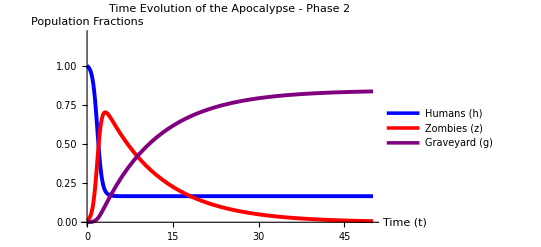

```mathematica
Clear[α, Δ, h, z, g, t, solution];
Δ = 3;        (* Attack Rate *)
α = 0.1;      (* Zombie Death Rate *)
c = 0.5;      (* Cure Rate*)

solution = NDSolve[
   {
    h'[t] == -Δ * h[t] * z[t] + c * z[t],
    z'[t] == -α * z[t] + Δ * h[t] * z[t] - c * z[t],
    g'[t] == α * z[t], 
    
    (* Initial Conditions *)
    h[0] == 1.0,
    z[0] == 0.01,
    g[0] == 0
   },
   {h, z, g},      
   {t, 0, 50}      
 ];

 (* 2. Plot *)
 Plot[
  Evaluate[{h[t], z[t], g[t]} /. solution],
  {t, 0, 50},
  
  PlotStyle -> {
    {Blue, Thickness[0.007]},
    {Red, Thickness[0.007]},
    {Purple, Thickness[0.007]}
  },
  PlotLegends -> {"Humans (h)", "Zombies (z)", "Graveyard (g)"},
  AxesLabel -> {"Time (t)", "Population Fractions"},
  PlotRange -> {0, 1.2}, 
  PlotLabel -> "Time Evolution of the Apocalypse - Phase 2"
 ]
```

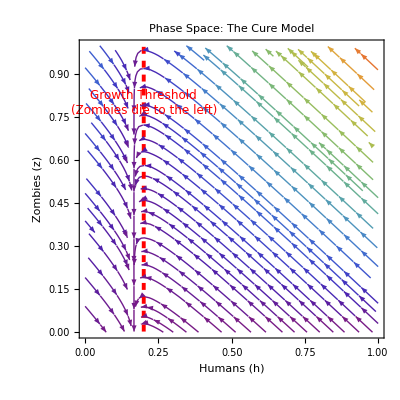

```mathematica
Module[{hCritical, hDot, zDot},
  
  (* 1. Define the Critical Human Population *)
  (* The cure (c) is added to the death rate (alpha), making the threshold harder for zombies to reach *)
  hCritical = (α + c) / Δ;
  
  (* 2. Define the Equations *)
  hDot = -(Δ * h * z) + (c * z);
  zDot = -(α * z) + (Δ * h * z) - (c * z);

  (* 3. Combine Plot and Line *)
  Show[
   (* The Flow Field *)
   StreamPlot[
    {hDot, zDot},
    {h, 0, 1}, {z, 0, 1},
    StreamColorFunction -> "Rainbow",
    FrameLabel -> {"Humans (h)", "Zombies (z)"},
    Frame -> True,
    LabelStyle -> {Bold, 14},
    PlotLabel -> Style["Phase Space: The Cure Model", 16, Bold]
   ],
   
   (* The Critical Threshold Line *)
   Graphics[{
     (* Red Dashed Line *)
     {Red, Dashed, Thickness[0.007], InfiniteLine[{{hCritical, 0}, {hCritical, 1}}]},
     
     (* Label *)
     Text[Style["Growth Threshold\n(Zombies die to the left)", Red, 12, Background -> White], 
      {hCritical, 0.8}, {-1.2, 0}]
    }],
    
   PlotRange -> {{0, 1}, {0, 1}}
  ]
 ]
```

## Phase 2.1 - Cure (might remove)

### Population-Time Graph

```mathematica
Manipulate[
 solution = NDSolve[
   {
    (* Humans: Lost to attack, gained from cure *)
    h'[t] == (-Δ * h[t]) * (z[t] + c * z[t]),
    z'[t] == (-α * z[t]) + (Δ * h[t] * z[t]) - (c * z[t]) + σ,
    g'[t] == α * z[t], 
    
    (* Initial Conditions *)
    h[0] == 1.0,
    z[0] == 0.01,
    g[0] == 0
   },
   {h, z, g},      
   {t, 0, 50}      
 ];

 (* 2. Plot *)
 Plot[
  Evaluate[{h[t], z[t], g[t]} /. solution],
  {t, 0, 50},
  
  PlotStyle -> {
    {Blue, Thickness[0.007]},
    {Red, Thickness[0.007]},
    {Purple, Thickness[0.007]}
  },
  PlotLegends -> {"Humans (h)", "Zombies (z)", "Graveyard (g)"},
  AxesLabel -> {"Time (t)", "Population Fractions"},
  PlotRange -> All, (* Changed to All because Z can grow > 1.2 with Sigma *)
  PlotLabel -> "Time Evolution: Constant Zombie Farming"
 ],

 (* 3. Sliders *)
 {{Δ, 2, "Attack Rate (Δ)"}, 0.1, 5, 0.01},
 {{α, 1, "Zombie Death Rate (α)"}, 0.1, 2, 0.01},
 {{c, 5, "Cure Rate (c)"}, 0, 2, 0.01},
 
 (* NEW: Farming Slider (Linear) *)
 Delimiter,
 {{σ, 4, "Farming Rate (σ)"}, 0, 1, 0.01}
]
```

### Phase Space

```mathematica
Manipulate[
 Module[{hDot, zDot, stableH, stableZ},
  
  (* 1. Define The Equations *)
  hDot = -Δ*h*z + c*z;
  zDot = Δ*h*z - α*z - c*z + (σ * z * (1 - z/K));
 
  (* 2. The Plot *)
  StreamPlot[
   {hDot, zDot},
   {h, 0, 10}, {z, 0, 10},
   Frame -> False,
   Axes -> True,
   AxesLabel -> {"Humans (h)", "Zombies (z)"},
   StreamColorFunction -> "Rainbow",
   
   PlotLabel -> Style["Stage 2: Logistic Zombie Farming", 14, Bold]
  ]
 ],
 
 (* Controls *)
 {{Δ, 1, "Attack rate (Δ)"}, 0.1, 5, 0.1},
 {{α, 0.5, "Zombie death rate (α)"}, 0.1, 2, 0.1},
 {{c, 2, "Cure rate (c)"}, 0.1, 5, 0.1}
]
```

## Phase 3 - Sustainable Farming

### Population-Time Plot

```mathematica
Manipulate[
 solution = NDSolve[
   {
    h'[t] == (σ * h[t] * (1 - h[t]/K)) - (Δ * h[t] * z[t]),
    z'[t] == (-α * z[t]) + (Δ * h[t] * z[t]),
    
    h[0] == 1.0,
    z[0] == 0.01
   },
   {h, z},
   {t, 0, 100}      
 ];

 (* Plot *)
 Plot[
  Evaluate[{h[t], z[t]} /. solution],
  {t, 0, 100},
  
  PlotStyle -> {
    {Blue, Thickness[0.007]},
    {Red, Thickness[0.007]}
  },
  
  PlotLegends -> {"Humans (h)", "Zombies (z)"}, 
  AxesLabel -> {"Time (t)", "Population Fractions"},
  PlotRange -> All, 
  PlotLabel -> "Time Evolution of the Apocalypse - Phase 3"
 ],

 (* Sliders *)
 {{Δ, 2, "Attack Rate (Δ)"}, 0.1, 2, 0.01},
 {{α, 1, "Zombie Death Rate (α)"}, 0.1, 1, 0.01},
 {{σ, 1, "Human Birth Rate (σ)"}, 0.1, 5, 0.01},
 {{K, 1, "Carrying Capacity (K)"}, 0.5, 5, 0.1}
]
```

### Phase Space

```mathematica
Manipulate[
 Module[{hDot, zDot, fixedPoints},
  
  (* h grows logistically on farm *)
  hDot = (σ * h * (1 - h/K)) - (Δ * h * z);
  zDot = (-α * z) + (Δ * h * z);
  
  Show[
   StreamPlot[
    {hDot, zDot},
    {h, 0, 1.2 * K}, {z, 0, 1.2 * K}, 
    StreamColorFunction -> "Rainbow",
    FrameLabel -> {"Humans (h)", "Zombies (z)"},
    Frame -> True,
    StreamPoints -> Fine,
    PlotLabel -> Style["Phase Space: Sustainable Farming", 16, Bold]
   ],
   
   (* 3. Mark the Saddle Point / Fixed Point at (K, 0) *)
   Graphics[(*{
     (*{Blue, PointSize[0.025], Point[{K, 0}]},
     {Text[Style["Disease Free\n(K, 0)", Blue, 12, Background -> White], {K, -0.1}]}*)
    }*)]
  ]
 ],
 
 (* Sliders *)
 (* High Delta = Saddle Point. Low Delta = Stable Node. *)
 {{Δ, 2, "Attack Rate (Δ)"}, 0.1, 5, 0.1},
 {{α, 1, "Zombie Death Rate (α)"}, 0.1, 2, 0.1},
 
 Delimiter,
 (* New Human Parameters *)
 {{σ, 1, "Human Birth Rate (σ)"}, 0.1, 2, 0.1},
 {{K, 1, "Carrying Capacity (K)"}, 1, 5, 0.5}
]
```

### Static Plotting for Report - Phase 3

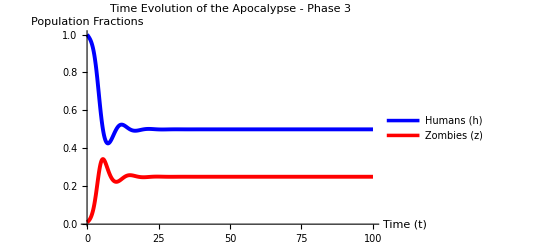

```mathematica
Clear[α, Δ, h, z, g, t, solution];
Δ = 2;      (* Attack Rate *)
α = 1;      (* Zombie Death Rate *)
σ = 1;      (* Human Farming Rate *)
K = 1;      (* Carrying Capacity *)

 solution = NDSolve[
   {
    h'[t] == (σ * h[t] * (1 - h[t]/K)) - (Δ * h[t] * z[t]),
    z'[t] == (-α * z[t]) + (Δ * h[t] * z[t]),
    
    h[0] == 1.0,
    z[0] == 0.01
   },
   {h, z},
   {t, 0, 100}      
 ];

 (* Plot *)
 Plot[
  Evaluate[{h[t], z[t]} /. solution],
  {t, 0, 100},
  
  PlotStyle -> {
    {Blue, Thickness[0.007]},
    {Red, Thickness[0.007]}
  },
  
  PlotLegends -> {"Humans (h)", "Zombies (z)"}, 
  AxesLabel -> {"Time (t)", "Population Fractions"},
  PlotRange -> All, 
  PlotLabel -> "Time Evolution of the Apocalypse - Phase 3"
 ]
```

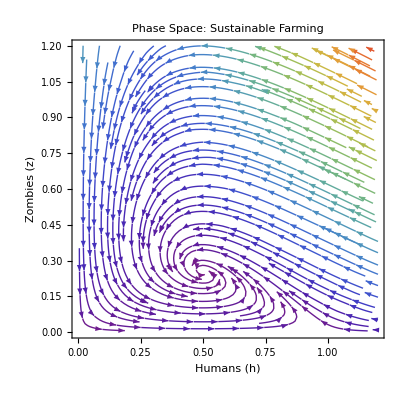

```mathematica
Clear[α, Δ, h, z, g, t, solution];
Δ = 2;      (* Attack Rate *)
α = 1;      (* Zombie Death Rate *)
σ = 1;      (* Human Farming Rate *)
K = 1;      (* Carrying Capacity *)

Module[{hDot, zDot, fixedPoints},
  
  hDot = (σ * h * (1 - h/K)) - (Δ * h * z);
  zDot = (-α * z) + (Δ * h * z);
  
  Show[
   StreamPlot[
    {hDot, zDot},
    {h, 0, 1.2 * K}, {z, 0, 1.2 * K}, 
    StreamColorFunction -> "Rainbow",
    FrameLabel -> {"Humans (h)", "Zombies (z)"},
    Frame -> True,
    StreamPoints -> Fine,
    PlotLabel -> Style["Phase Space: Sustainable Farming", 16, Bold]
   ]
  ]
 ]
```

### Bifurcations

```mathematica
Manipulate[
 Module[{sol, h, z, t},
  (* Solve the system *)
  sol = NDSolve[{
     h'[t] == (σ * h[t] * (1 - h[t]/K)) - (Δ * h[t] * z[t]),
     z'[t] == -α * z[t] + Δ * h[t] * z[t],
     h[0] == 0.1 * K, z[0] == 0.1 * K (* Start low to see the spiral grow *)
    }, {h, z}, {t, 0, 100}][[1]];

  (* Show Parametric Plot on top of StreamPlot *)
  Show[
   StreamPlot[
    {
     (σ * h * (1 - h/K)) - (Δ * h * z),
     -α * z + Δ * h * z
    },
    {h, 0, 1.2 * K}, {z, 0, 1.2 * K},
    StreamColorFunction -> "Rainbow",
    StreamStyle -> LightGray
   ],
   
   ParametricPlot[
    Evaluate[{h[t], z[t]} /. sol], {t, 0, 100},
    PlotStyle -> {Red, Thickness[0.006]},
    PlotRange -> {{0, 1.2*K}, {0, 1.2*K}}
   ],
   
   Frame -> True,
   FrameLabel -> {"Humans", "Zombies"},
   PlotLabel -> "Phase Space"
  ]
 ],
 
 (* Sliders tuned to show spiraling *)
 {{Δ, 2, "Attack Rate(Δ)"}, 0.5, 5},
 {{α, 1, "Zombie Death(α)"}, 0.1, 2},
 {{σ, 1, "Human Birth (σ)(Low = More Spirals)"}, 0.1, 2},
 {{K, 1, "Carrying Capacity (K)(High = More Spirals)"}, 1, 10}
]
```

```mathematica
Manipulate[
 Module[{xDot},
  
  xDot[x_] := r * x - x^2;

  Show[
   Plot[xDot[x], {x, -4, 4},
    PlotStyle -> {Blue, Thickness[0.005]},
    PlotRange -> {{-4, 4}, {-4, 4}},
    AxesLabel -> {"x (Population)", "x' (Growth Rate)"},
    AxesOrigin -> {0, 0},
    Filling -> Axis,
    FillingStyle -> Opacity[0.1, Blue]
   ],
   
   (* Vector Field *)
   StreamPlot[
    {xDot[x], 0}, 
    {x, -4, 4}, {y, -0.5, 0.5},
    StreamPoints -> Fine,
    StreamStyle -> {Red, Arrowheads[0.03]}
   ],
   
   (* Dynamic Fixed Points *)
   Graphics[{
     
     (* --- POINT AT x = 0 (The Origin) --- *)
     (* Stability Condition: Stable if r < 0 *)
     If[r < 0,
        (* If Stable: Solid Black *)
        {Black, PointSize[0.035], Point[{0, 0}]},
        (* If Unstable: Hollow (Black with White Center) *)
        {Black, PointSize[0.035], Point[{0, 0}], White, PointSize[0.025], Point[{0, 0}]}
     ],
     
     (* --- POINT AT x = r (The Bifurcation Point) --- *)
     (* Stability Condition: Stable if r > 0 *)
     If[r > 0,
        (* If Stable: Solid Black *)
        {Black, PointSize[0.035], Point[{r, 0}]},
        (* If Unstable: Hollow *)
        {Black, PointSize[0.035], Point[{r, 0}], White, PointSize[0.025], Point[{r, 0}]}
     ],
     
     Text[Style[If[r < 0, "Stable", "Unstable"], 11, Background->White], {0, 0.5}],
     Text[Style[If[r > 0, "Stable", "Unstable"], 11, Background->White], {r, -0.5}]
    }]
   ]
  ],
 
 (* Controls *)
 {{r, -1.5, "Parameter (r)"}, -3, 3, 0.1, Appearance -> "Labeled"},
 TrackedSymbols :> {r}
]
```

```mathematica
Manipulate[
 Module[{r},
  r[z_] := (1/K) - (2 * z);
  
  Plot[r[z], {z, 0, 1},
   PlotStyle -> {Red, Thickness[0.007]},
   AxesLabel -> {"Zombie Density (z)", "Net Human Growth (r)"},
   PlotRange -> {{0, 1}, {-1, 1}},
   Filling -> Axis,
   FillingStyle -> {
     1 -> Opacity[0.2, Blue],  (* Positive r = Humans Surplus *)
     -1 -> Opacity[0.2, Red]   (* Negative r = Human Shortage *)
   },
   
   (* Show the Tipping Point *)
   Epilog -> {
     {Black, Dashed, InfiniteLine[{{1/(2*K), -1}, {1/(2*K), 1}}]},
     {Text[Style["Tipping Point\nz = " <> ToString[NumberForm[1/(2*K), 2]], Black, 12, Background -> White], {1/(2*K) + 0.15, 0.5}]}
   },
   
   PlotLabel -> "Stability Analysis: r = (1/K) - 2z"
  ]
 ],
 
 {{K, 1, "Island Capacity (K)"}, 0.5, 2, 0.1}
]
```